# NG22P06. Метод опорных векторов: ядра и штрафы

### 1. Последовательный метод активных ограничений

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Dimensions[Train=Rest[Import["NG22P06Problem.xlsx",{"Sheets","Гуд"}]]];
```

```mathematica
X=Train⟦;;,{1,2}⟧;
Y = Train⟦;;,3⟧//Round;
```

```mathematica
iCold = Flatten[Position[Y,-1]];
iWarm = Flatten[Position[Y,1]];
```

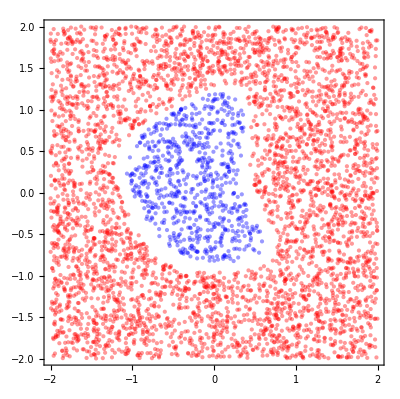

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},Opacity[0.4],Point[#1]}&,{X,Y}],
Frame->True
]
```

```mathematica
ClearAll[kmIncAS];
kmIncAS[Sigma_,surCharge_,counter_]:=Quiet@Monitor[
  kmInit[Sigma,surCharge,counter];
  While[State≠"Stop",Switch[State,
    "SVM",  ΛS=kmSolveQP[]; SVM=kmSVM[kmW0[]]; Step++; State="S➫O"; Fig=kmFig[],
    "S➫O", State=If[kmDone@"S➫O", "SVM", "S➫C" ],
    "S➫C", State=If[kmDone@"S➫C", "SVM", "O➫S" ],
    "O➫S", State=If[kmDone@"O➫S", "SVM", "C➫S" ],
    "C➫S", State=If[kmDone@"C➫S", "SVM", "Stop" ]
]];Fig,Fig]
```

```mathematica
(*Исходные данные*)
```

Train - матрица данных о точках, включающая в себя координаты точек и метки. Метка может быть -1 (холодный класс) или 1 (теплый класс). Для удобства разбивается на переменные X и Y
X, Y - координаты точек и соответствущие им метки
iCold, iWarm - список индексов точек (в обучающем наборе) холодного и теплого класса соответственно.

```mathematica
(*Входные параметры алгоритма*)
```

Sigma (σ) - характеризующий размер зоны влияния функции Гаусса
surCharge (𝒞) - значение штрафа, который дается точкам, не принадлежащим своему классу
counter - количество изначальных опорных точек

```mathematica
(*Процедурные блоки (подпрограммы)*)
```

kmIncAS - функция, с помощью которой реализуется обучение классификатора - решение квадратичной задачи оптимизации, перенос точек из одного класса в другой, а также построение графика фазового пространства с текущими точками и разделяющией линией классификатора
kmInit - инициализация параметров алгоритма, необходимых для обучения - входные параметры, начальное множества опорных, внешних и точек - нарушителей, значение матрицы Q, ядро
kmKer - компилируемая функция, в основу которой лежит функция Гаусса. Является ядром
kmSupport - нахождение изначального множетсва опорных точек
kmProblemQP - описание задачи квадратичной оптимизации, включающей в себя саму функцию, минимимум которой необходимо найти, а также ограничивающие условия для множителей Лагранжа
kmSolveQP - решение задачи квадратичной оптимизации, т.е. поиск множителей Лагранжа, при которых функция достигает своего минимума
kmW0 - вычисление веса - сдвига W0 для SVM классификатора
kmSVM - компилируемая функция SVM классификатора по значению W0 и по текущему множеству опорных точек и точек - нарушителей
kmFig - график фазового пространства, на котором изображены текущие множества опорных, внешних и точек - нарушителей и разделяющая линия классификатора
kmDone - проверка множества точек на необходимость их переноса из одной группы (опорных, внешних или нарушителей) в другой

```mathematica
(*Глобальные переменные*)
```

State - значение статуса алгоритма, т.е. решение задачи оптимизации, перенос точек из одних множеств в другие или остановка алгоритма
Step - шаг алгоритма
σ - размер зоны влияния функции Гаусса
𝒞 - штраф
Fig - график фазового пространства с текущими множествами точек и значениями классификатора
iS, iO, iC - множества опорных точек, внешних точек и точек - нарушителей соотвественно
Qss, Qcs - значения матриц, необходимых для решения задачи оптимизацией, поставленной в матричном виде
Λ - множители Лагранжа в символьном виде
ΛS - числовые значения множителей Лагранжа
SVM - классификтор, построенный по текущим значениям множителей Лагранжа  и множествам опорных и точек - нарушителей
X - значения координат точек
Y - метки точек
x1Min, x1Max, x2Min, x2Max - границы графика фазового пространства

### 2. Ядро и инициализация опорных точек

```mathematica
(*Т.к. для алгоритма нужна не вся матрица Q, а только ее два блока, их и инициализируем*)
```

```mathematica
ClearAll[kmInit];
kmInit[Sigma_,surCharge_,counter_]:=(
State="SVM"; Step=0; σ=Sigma; 𝒞=surCharge; Fig=Fig0;
Ker=kmKer[Sigma];
iS=kmSupport[counter]; iC={}; iO=Complement[Range[Length[X]],iS];
Qss=ParallelArray[Y⟦iS⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}];
Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}];
Fig=kmFig[];
);
```

```mathematica
ClearAll[kmKer];
kmKer[σ_]:=Compile[
{{x,_Real,1},{y,_Real,1}},
Exp[-((x-y).(x-y))/(2 σ^2)],
Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"
];
```

```mathematica
(*σ=0.4 подходит*)
```

```mathematica
Ker=kmKer[0.4];
```

```mathematica
Plot3D[Ker[{x,y},Mean[X]],{x,-2,2},{y,-2,2},ColorFunction->"GreenPinkTones",PlotRange->All]
```

-Graphics3D-

```mathematica
(*Инициализация начального множества опорных точек*)
```

```mathematica
ClearAll[kmSupport]; (** ↦ iS **)
kmSupport[counter_]:=Module[
{iSC,iSW,iS={},step=0},
While[
step++<counter∧Length@iS<counter,
iSC=RandomSample[iCold,1];
iSC=FixedPoint[(iSW=First[Nearest[X⟦iWarm⟧->iWarm,X⟦#⟧]];
First[Nearest[X⟦iCold⟧->iCold,X⟦iSW⟧]])&,iSC];
iS=Join[iS,iSW,iSC];
iS=DeleteDuplicates[iS];
];
Return[iS];
]
```

```mathematica
iS=kmSupport[20];
iC={};
```

```mathematica
(*График опорных точек*)
```

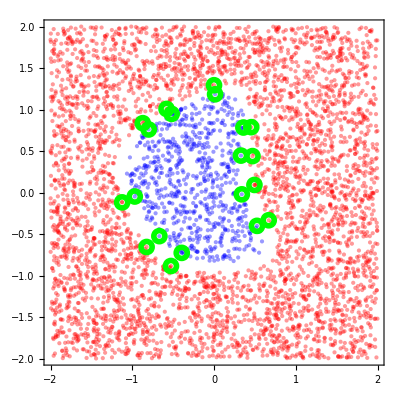

```mathematica
Show[
Fig0,
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics
]
```

### 3. Решение задачи квадратичного программирования

```mathematica
(*Для задачи нужно считать Qss и Qcs каждый раз*)
```

```mathematica
ClearAll[kmProblemQP];
kmProblemQP[]:= 
Chop@Flatten@{
Λ=Array[Subscript[λ, #]&,Length@iS];
Qss=ParallelArray[Y⟦iS⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}];
Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}];
1/2 Qss.Λ.Λ + If[Length[Qcs]≠0,𝒞 Total[Qcs.Λ],0]-Total[Λ],
And@@Append[Map[#≥-10&,Λ],Y⟦iS⟧.Λ+𝒞 Total[Y⟦iC⟧]==0]
};
```

```mathematica
ClearAll[kmSolveQP]; (** ↦ ΛS **)
kmSolveQP[]:= With[{prob=kmProblemQP[]},Values@Last@FindMinimum[prob,Λ]];
```

```mathematica
𝒞=0;
```

```mathematica
ΛS=kmSolveQP[]
```

{24.3562,22.0194,9.09389,9.66675,12.4106,15.0927,-10.,-7.67509,13.4837,11.9714,6.74874,5.75791,4.80558,4.53436,1.96324,2.90925,34.9659,33.6984,7.73554,7.58824}

```mathematica
(*Условия в задаче - ограничиваем лямбды снизу*)
```

```mathematica
And@@Append[Map[#≥-10&,Λ],Y⟦iS⟧.Λ+𝒞 Total[Y⟦iC⟧]==0]
```

λ_1≥-10&&λ_2≥-10&&λ_3≥-10&&λ_4≥-10&&λ_5≥-10&&λ_6≥-10&&λ_7≥-10&&λ_8≥-10&&λ_9≥-10&&λ_10≥-10&&λ_11≥-10&&λ_12≥-10&&λ_13≥-10&&λ_14≥-10&&λ_15≥-10&&λ_16≥-10&&λ_17≥-10&&λ_18≥-10&&λ_19≥-10&&λ_20≥-10&&λ_1-λ_2+λ_3-λ_4+λ_5-λ_6+λ_7-λ_8+λ_9-λ_10+λ_11-λ_12+λ_13-λ_14+λ_15-λ_16+λ_17-λ_18+λ_19-λ_20==0

### 4. SVM-классификатор

```mathematica
(*Значение W0*)
```

```mathematica
ClearAll[kmW0];
kmW0[]:= Median[
   Dot[Join[ΛS Y⟦iS⟧,𝒞 Y⟦iC⟧],Ker[X⟦Join[iS,iC]⟧,#]]&/@X⟦iS⟧-Y⟦iS⟧
];
```

```mathematica
kmW0[]
```

-0.931488

```mathematica
(*SVM-классификатор*)
```

```mathematica
ClearAll[kmSVM];
kmSVM[w0_]:= With[
  {ΛYsc=Join[ΛS Y⟦iS⟧,𝒞 Y⟦iC⟧],
   Xsc=X⟦Join[iS,iC]⟧},
  Compile[
{{x,_Real,1}},
ΛYsc.Ker[Xsc,x]-w0,
Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"
]
];
```

```mathematica
SVM=kmSVM[kmW0[]]
```

CompiledFunction[…]

```mathematica
Plot3D[SVM[{x,y}],{x,-2,2},{y,-2,2},ColorFunction->"GreenPinkTones",PlotRange->All]
```

-Graphics3D-

### 5. Карта разделяющей полосы

```mathematica
kmInit[0.4,100,20];
```

```mathematica
ClearAll[kmFig];
kmFig[]:=Show[
Fig0,
ContourPlot[
SVM@{x1,x2},{x1,x1Min,x1Max},{x2,x2Min,x2Max},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.1],Blue},Opacity[0],Opacity[0],{Opacity[0.1],Red}}
],
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics,
{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧//Graphics,
    PlotLabel->StringForm["Step=``,σ=``,C=``,iS=``,iC=``,iO=``",Step,σ,𝒞,Length@iS,Length@iC,Length@iO]
];
```

```mathematica
x1Min=x2Min=-2;
x1Max=x2Max=2;
```

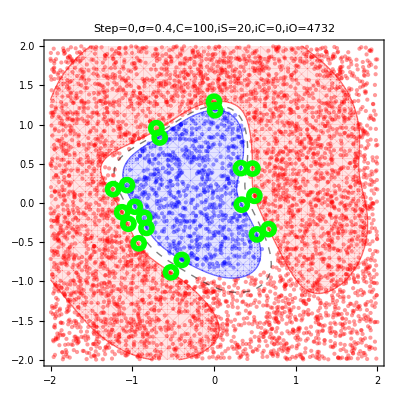

```mathematica
kmFig[]
```

### 6. Корректировка множества опорных точек

```mathematica
(** Support ⟶ Outlier **)
ClearAll[kmDone];
kmDone["S➫O"]:=If[
  Length@iS < 2 ∨ 0 == Length[iBad=Flatten@Position[ΛS,_?NonPositive,{1}]],
  (***)False,
    iBad = RandomChoice[Abs[ΛS⟦iBad⟧]->iBad];
    Fig = Show[Fig,Graphics[{Black,AbsoluteThickness[4],Circle[X⟦iS⟦iBad⟧⟧,Offset[4]]}]];
    AppendTo[iO,iS⟦iBad⟧];
    iS = Delete[iS,iBad];
  (***)True
];
```

```mathematica
(** Support ⟶ Cost **)
kmDone["S➫C"]:=If[
  Length@iS < 2 ∨ 0 == Length[iBad=Flatten@Position[ΛS,_?NonPositive,{1}]],
  (***)False,
    iBad = RandomChoice[Abs[ΛS⟦iBad⟧]->iBad];
    Fig = Show[Fig,Graphics[{Black,AbsoluteThickness[4],Circle[X⟦iS⟦iBad⟧⟧,Offset[4]]}]];
    AppendTo[iC,iS⟦iBad⟧];
    iS = Delete[iS,iBad];
  (***)True
];
```

### 7. Проверка отступа неопорных точек

```mathematica
(*Отступы*)
```

```mathematica
ClearAll[kmMargin];
kmMargin[ind_List]:=Y⟦#⟧SVM[X⟦#⟧]&/@ind;
kmMargin[ind_]:=Y⟦ind⟧SVM[X⟦ind⟧];
```

```mathematica
(** Outlier ⟶ Support **)
kmDone["O➫S"]:=If[
  M = kmMargin[iO];
  0 == Length[iBad=Flatten@Position[M,_?(#<1&),{1}]],
  (***)False,
    iBad = RandomChoice[Abs[M⟦iBad⟧]->iBad];
    Fig = Show[Fig,Graphics[{Black,AbsoluteThickness[4],Circle[X⟦iO⟦iBad⟧⟧,Offset[4]]}]];
    AppendTo[iS,iO⟦iBad⟧];
    iO = Delete[iO,iBad];
  (***)True
];
```

```mathematica
(** Cost ⟶ Support **)
kmDone["C➫S"]:=If[
  M = kmMargin[iC];
  iC =={} ∨ 0 == Length[iBad=Flatten@Position[M,_?(#>1&),{1}]],
  (***)False,
    iBad = RandomChoice[Abs[M⟦iBad⟧]->iBad];
    Fig = Show[Fig,Graphics[{Black,AbsoluteThickness[4],Circle[X⟦iC⟦iBad⟧⟧,Offset[4]]}]];
    AppendTo[iS,iC⟦iBad⟧];
    iC = Delete[iC,iBad];
  (***)True
];
```

### 8. Обучение SVM-классификатора

```mathematica
(*В результате не было никаких точек-нарушителей - алгоритм смог построить разделяющую линию, которая точно разделяет между двумя классами. Это может отчасти быть потому что фигура, построенная точками холодного класса, довольно простая, а также отчасти потому что значение штрафа большое*)
```

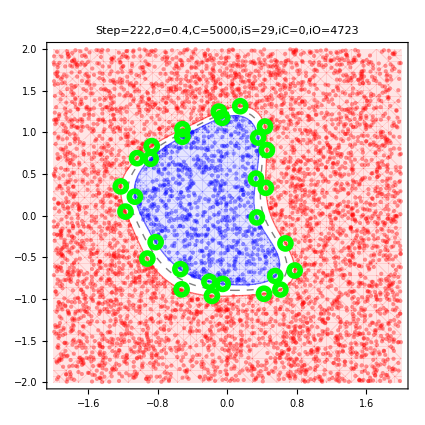

```mathematica
kmIncAS[0.4,5000,10]
```